```mathematica
vmax=11;
p=0.1;
rho=Round[(1-p)/(vmax+1-2*p),0.001];
dmin=Round[rho*0.1,0.001];
dmax=Round[rho*1.2,0.001];
dd=Round[(dmax-dmin)/22,0.001];
rho " :Transition density!!!"
dmin ": Min density"
dmax ": Max density"
dd ": density step"
"List of simulated values:"
For[i=-1,i<20,i++;
Print[dmin+i*dd]
]
For[i=1,i<4,i++;
Print[i*rho]
]
```

0.076  :Transition density!!!

0.008 : Min density

0.091 : Max density

0.004 : density step

List of simulated values:

0.008

0.012

0.016

0.02

0.024

0.028

0.032

0.036

0.04

0.044

0.048

0.052

0.056

0.06

0.064

0.068

0.072

0.076

0.08

0.084

0.088

0.152

0.228

0.304

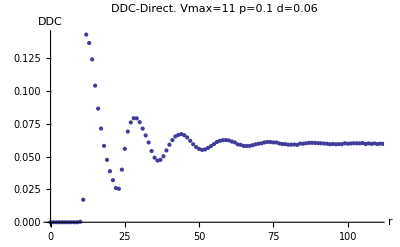

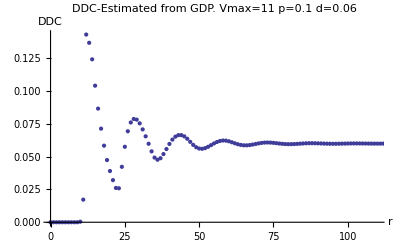

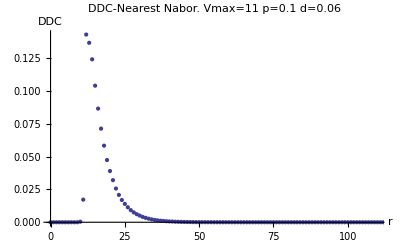

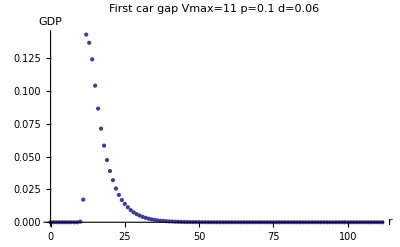

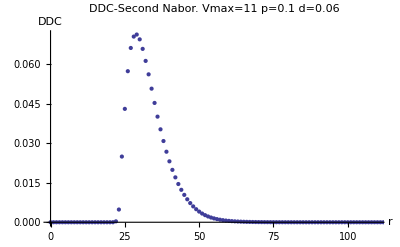

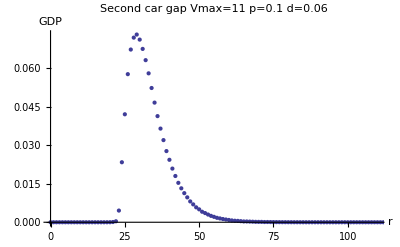

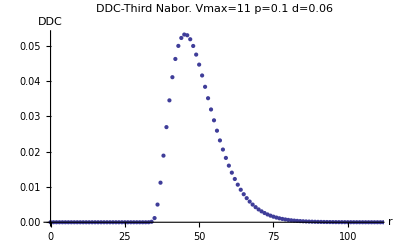

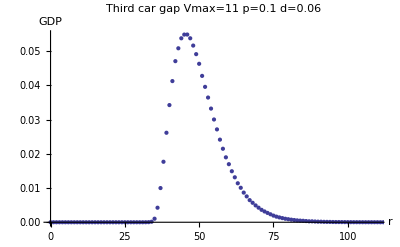

--------------------------------------------------------------------------------------

```mathematica
d="0.06";
p="0.1";
vmax="11";
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/ddensitycorrelation.d";
ddc1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC1.d";ddc2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC2.d";
ddc3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC3.d";
gap1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/GapD.d.";
gap2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/Gap2D.d.";
gap3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/Gap3D.d.";
g=".p"<>p<>".v11.txt";

ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
ddc1add=ddc1<>d<>g;
ddc2add=ddc2<>d<>g;
ddc3add=ddc3<>d<>g;
gap1add=gap1<>d<>g;
gap2add=gap2<>d<>g;
gap3add=gap3<>d<>g;
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
DDC1=ReadList[ddc1add,{Number,Number}];
DDC2=ReadList[ddc2add,{Number,Number}];
DDC3=ReadList[ddc3add,{Number,Number}];
GAP1=ReadList[gap1add,{Number,Number}];
GAP2=ReadList[gap2add,{Number,Number}];
GAP3=ReadList[gap3add,{Number,Number}];
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDC1,PlotLabel->"DDC-Nearest Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP1,PlotLabel->"First car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC2,PlotLabel->"DDC-Second Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP2,PlotLabel->"Second car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC3,PlotLabel->"DDC-Third Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP3,PlotLabel->"Third car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[{DDC,DDC1},PlotLabel->"DDC-(Direct vs. First Nabor).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
SDDC1=DDC1[[All,2]];
SDDC2=DDC2[[All,2]];
SDDC3=DDC3[[All,2]];
SGAP1=GAP1[[All,2]];
SGAP2=GAP2[[All,2]];
SGAP3=GAP3[[All,2]];
Com2=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]},{i,1,220}];
Com3=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]+SDDC3[[i]]},{i,1,220}];
Com2Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]},{i,1,220}];
Com3Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]+SGAP3[[i]]},{i,1,220}];
ListPlot[{DDC,Com2,Com2Gap},PlotLabel->"DDC-(Direct vs. First Two Nabors vs. First Two Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated  vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,10},Full}]
"--------------------------------------------------------------------------------------"
```

ListPlot[$Failed,PlotLabel→DDC-Direct.  Vmax=11  p=0.1 d=0.08,AxesLabel→{r,DDC},PlotRange→{{0,110},Full}]

ListPlot[$Failed,PlotLabel→DDC-Estimated from GDP.  Vmax=11  p=0.1 d=0.08,AxesLabel→{r,DDC},PlotRange→{{0,110},Full}]

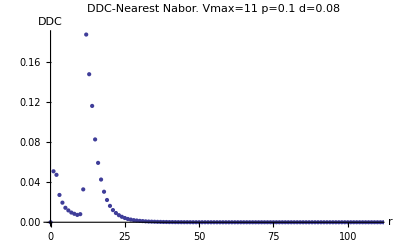

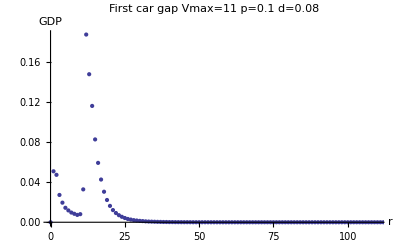

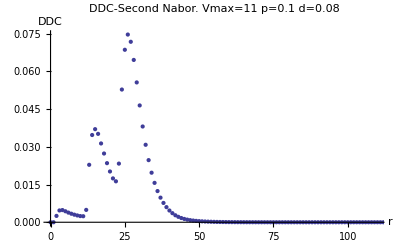

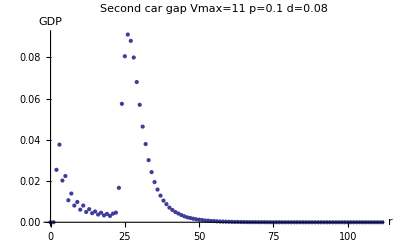

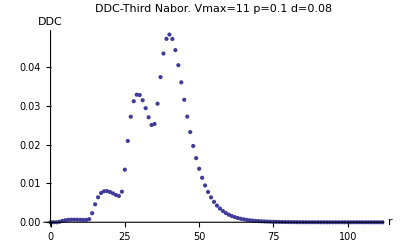

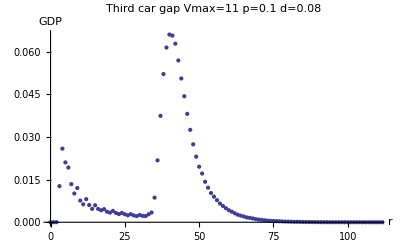

ListPlot[{$Failed,{{0,0},{1,0.0509779},{2,0.0474298},{3,0.0273023},{4,0.0196},{5,0.014474},{6,0.0118412},{7,0.00971221},{8,0.00845573},{9,0.00734351},{10,0.00809618},{11,0.032884},{12,0.187776},{13,0.148084},{14,0.116376},{15,0.0828557},{16,0.0593908},{17,0.0427336},{18,0.0305366},{19,0.0222618},{20,0.016371},{21,0.0121718},{22,0.00922901},{23,0.00706336},{24,0.00545344},{25,0.00424504},{26,0.00329466},{27,0.00266336},{28,0.00209618},{29,0.00173359},{30,0.00137557},{31,0.00115573},{32,0.000885496},{33,0.000710687},{34,0.000606107},{35,0.000506107},{36,0.000405344},{37,0.000338168},{38,0.000266412},{39,0.000249618},{40,0.000173282},{41,0.000164885},{42,0.000116794},{43,0.00010458},{44,0.0000816794},{45,0.0000625954},{46,0.0000748092},{47,0.000051145},{48,0.0000358779},{49,0.0000328244},{50,0.0000290076},{51,0.000019084},{52,0.0000198473},{53,0.0000160305},{54,7.63359×10^-6},{55,0.0000122137},{56,9.16031×10^-6},{57,4.58015×10^-6},{58,6.10687×10^-6},{59,6.10687×10^-6},{60,6.87023×10^-6},{61,7.63359×10^-7},{62,7.63359×10^-7},{63,2.29008×10^-6},{64,2.29008×10^-6},{65,7.63359×10^-7},{66,2.29008×10^-6},{67,0},{68,7.63359×10^-7},{69,0},{70,0},{71,0},{72,7.63359×10^-7},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0},{83,7.63359×10^-7},{84,0},{85,0},{86,7.63359×10^-7},{87,0},{88,0},{89,0},{90,0},{91,0},{92,0},{93,0},{94,0},{95,0},{96,0},{97,0},{98,0},{99,0},{100,0},{101,0},{102,0},{103,0},{104,0},{105,0},{106,0},{107,0},{108,0},{109,0},{110,0},{111,0},{112,0},{113,0},{114,0},{115,0},{116,0},{117,0},{118,0},{119,0},{120,0},{121,0},{122,0},{123,0},{124,0},{125,0},{126,0},{127,0},{128,0},{129,0},{130,0},{131,0},{132,0},{133,0},{134,0},{135,0},{136,0},{137,0},{138,0},{139,0},{140,0},{141,0},{142,0},{143,0},{144,0},{145,0},{146,0},{147,0},{148,0},{149,0},{150,0},{151,0},{152,0},{153,0},{154,0},{155,0},{156,0},{157,0},{158,0},{159,0},{160,0},{161,0},{162,0},{163,0},{164,0},{165,0},{166,0},{167,0},{168,0},{169,0},{170,0},{171,0},{172,0},{173,0},{174,0},{175,0},{176,0},{177,0},{178,0},{179,0},{180,0},{181,0},{182,0},{183,0},{184,0},{185,0},{186,0},{187,0},{188,0},{189,0},{190,0},{191,0},{192,0},{193,0},{194,0},{195,0},{196,0},{197,0},{198,0},{199,0},{200,0},{201,0},{202,0},{203,0},{204,0},{205,0},{206,0},{207,0},{208,0},{209,0},{210,0},{211,0},{212,0},{213,0},{214,0},{215,0},{216,0},{217,0},{218,0},{219,0}}},PlotLabel→DDC-(Direct vs. First Nabor).  Vmax=11  p=0.1 d=0.08,AxesLabel→{r,DDC},PlotRange→{{0,220},Full}]

ListPlot[{$Failed,{{0,0},{1,0.0509779},{2,0.0499546},{3,0.031995},{4,0.0244487},{5,0.0188471},{6,0.0156835},{7,0.0131059},{8,0.0114715},{9,0.0100553},{10,0.0105538},{11,0.0352816},{12,0.192695},{13,0.170938},{14,0.151083},{15,0.119886},{16,0.0945557},{17,0.0740807},{18,0.0578823},{19,0.045771},{20,0.0365679},{21,0.0296166},{22,0.0255177},{23,0.0303941},{24,0.058253},{25,0.072861},{26,0.0779676},{27,0.0744608},{28,0.0666702},{29,0.0573613},{30,0.0478476},{31,0.0392509},{32,0.0317058},{33,0.0254238},{34,0.0203194},{35,0.0161715},{36,0.012813},{37,0.0101284},{38,0.00795021},{39,0.00626502},{40,0.00484505},{41,0.00377687},{42,0.00289741},{43,0.00226468},{44,0.00176379},{45,0.00138205},{46,0.00112118},{47,0.000889322},{48,0.000709709},{49,0.000577137},{50,0.000469453},{51,0.000381017},{52,0.000313037},{53,0.00025742},{54,0.000203673},{55,0.000172725},{56,0.000140092},{57,0.000111452},{58,0.0000967051},{59,0.0000810515},{60,0.0000681133},{61,0.0000513338},{62,0.0000424713},{63,0.0000360065},{64,0.0000303262},{65,0.000023905},{66,0.0000206152},{67,0.0000154899},{68,0.0000135423},{69,0.0000101747},{70,8.48311×10^-6},{71,7.26404×10^-6},{72,7.16497×10^-6},{73,4.8448×10^-6},{74,3.67928×10^-6},{75,3.02646×10^-6},{76,2.55816×10^-6},{77,2.03476×10^-6},{78,1.83614×10^-6},{79,1.3485×10^-6},{80,1.09461×10^-6},{81,7.76257×10^-7},{82,5.51774×10^-7},{83,1.16766×10^-6},{84,4.42837×10^-7},{85,3.27847×10^-7},{86,9.94228×10^-7},{87,1.97663×10^-7},{88,1.45124×10^-7},{89,9.59522×10^-8},{90,6.64829×10^-8},{91,4.6939×10^-8},{92,3.33882×10^-8},{93,2.50141×10^-8},{94,3.79754×10^-8},{95,1.52416×10^-7},{96,1.20507×10^-7},{97,1.14015×10^-7},{98,2.05922×10^-7},{99,1.57154×10^-7},{100,1.19744×10^-7},{101,8.45151×10^-8},{102,6.00911×10^-8},{103,4.28526×10^-8},{104,3.03173×10^-8},{105,2.17411×10^-8},{106,1.55818×10^-8},{107,1.11405×10^-8},{108,7.96683×10^-9},{109,5.58455×10^-9},{110,3.87108×10^-9},{111,2.5136×10^-9},{112,1.5098×10^-9},{113,8.68993×10^-10},{114,4.35369×10^-10},{115,1.58159×10^-10},{116,0},{117,0},{118,0},{119,0},{120,0},{121,0},{122,0},{123,0},{124,0},{125,0},{126,0},{127,0},{128,0},{129,0},{130,0},{131,0},{132,0},{133,0},{134,0},{135,0},{136,0},{137,0},{138,0},{139,0},{140,0},{141,0},{142,0},{143,0},{144,0},{145,0},{146,0},{147,0},{148,0},{149,0},{150,0},{151,0},{152,0},{153,0},{154,0},{155,0},{156,0},{157,0},{158,0},{159,0},{160,0},{161,0},{162,0},{163,0},{164,0},{165,0},{166,0},{167,0},{168,0},{169,0},{170,0},{171,0},{172,0},{173,0},{174,0},{175,0},{176,0},{177,0},{178,0},{179,0},{180,0},{181,0},{182,0},{183,0},{184,0},{185,0},{186,0},{187,0},{188,0},{189,0},{190,0},{191,0},{192,0},{193,0},{194,0},{195,0},{196,0},{197,0},{198,0},{199,0},{200,0},{201,0},{202,0},{203,0},{204,0},{205,0},{206,0},{207,0},{208,0},{209,0},{210,0},{211,0},{212,0},{213,0},{214,0},{215,0},{216,0},{217,0},{218,0},{219,0}},{{0,0},{1,0.0509779},{2,0.072858},{3,0.0649412},{4,0.0398443},{5,0.0368977},{6,0.0224969},{7,0.0236382},{8,0.0165618},{9,0.017171},{10,0.0141977},{11,0.0409886},{12,0.192778},{13,0.154437},{14,0.120774},{15,0.0880893},{16,0.063129},{17,0.0473496},{18,0.0338664},{19,0.0263091},{20,0.0194321},{21,0.0163344},{22,0.0139},{23,0.0237542},{24,0.0628916},{25,0.0847343},{26,0.0943123},{27,0.0906306},{28,0.0819748},{29,0.0697229},{30,0.0583321},{31,0.0475267},{32,0.0388008},{33,0.0308359},{34,0.0249176},{35,0.0199779},{36,0.0162595},{37,0.0132321},{38,0.0107603},{39,0.00904275},{40,0.00727175},{41,0.0061252},{42,0.00506335},{43,0.00434809},{44,0.00359695},{45,0.0029542},{46,0.0024458},{47,0.00212595},{48,0.00175573},{49,0.00146793},{50,0.00125496},{51,0.00109618},{52,0.000855725},{53,0.000796184},{54,0.000620611},{55,0.000590077},{56,0.000464885},{57,0.000367939},{58,0.000314504},{59,0.00029313},{60,0.000253435},{61,0.000199236},{62,0.000154961},{63,0.000155725},{64,0.000123664},{65,0.0000992367},{66,0.0000824428},{67,0.0000633588},{68,0.0000541985},{69,0.0000541985},{70,0.0000450382},{71,0.0000442748},{72,0.0000396947},{73,0.0000183206},{74,0.0000175573},{75,0.0000206107},{76,0.0000137405},{77,0.0000122137},{78,0.0000114504},{79,7.63359×10^-6},{80,6.87023×10^-6},{81,3.81679×10^-6},{82,3.81679×10^-6},{83,7.63359×10^-6},{84,2.29008×10^-6},{85,3.81679×10^-6},{86,4.58015×10^-6},{87,7.63359×10^-7},{88,0},{89,1.52672×10^-6},{90,0},{91,7.63359×10^-7},{92,7.63359×10^-7},{93,0},{94,0},{95,7.63359×10^-7},{96,0},{97,0},{98,0},{99,7.63359×10^-7},{100,1.52672×10^-6},{101,0},{102,0},{103,7.63359×10^-7},{104,0},{105,0},{106,0},{107,0},{108,0},{109,0},{110,0},{111,0},{112,0},{113,0},{114,0},{115,0},{116,0},{117,0},{118,0},{119,0},{120,0},{121,0},{122,0},{123,0},{124,0},{125,0},{126,0},{127,0},{128,0},{129,0},{130,0},{131,0},{132,0},{133,0},{134,0},{135,0},{136,0},{137,0},{138,0},{139,0},{140,0},{141,0},{142,0},{143,0},{144,0},{145,0},{146,0},{147,0},{148,0},{149,0},{150,0},{151,0},{152,0},{153,0},{154,0},{155,0},{156,0},{157,0},{158,0},{159,0},{160,0},{161,0},{162,0},{163,0},{164,0},{165,0},{166,0},{167,0},{168,0},{169,0},{170,0},{171,0},{172,0},{173,0},{174,0},{175,0},{176,0},{177,0},{178,0},{179,0},{180,0},{181,0},{182,0},{183,0},{184,0},{185,0},{186,0},{187,0},{188,0},{189,0},{190,0},{191,0},{192,0},{193,0},{194,0},{195,0},{196,0},{197,0},{198,0},{199,0},{200,0},{201,0},{202,0},{203,0},{204,0},{205,0},{206,0},{207,0},{208,0},{209,0},{210,0},{211,0},{212,0},{213,0},{214,0},{215,0},{216,0},{217,0},{218,0},{219,0}}},PlotLabel→DDC-(Direct vs. First Two Nabors vs. First Two Gaps).  Vmax=11  p=0.1 d=0.08,AxesLabel→{r,DDC},PlotRange→{{0,220},Full}]

ListPlot[{$Failed,{{0,0},{1,0.0509779},{2,0.0499546},{3,0.0321163},{4,0.0248015},{5,0.0193759},{6,0.0163063},{7,0.0137619},{8,0.0121326},{9,0.0107043},{10,0.0111854},{11,0.0358916},{12,0.193295},{13,0.171729},{14,0.153408},{15,0.124506},{16,0.100995},{17,0.0816248},{18,0.0658805},{19,0.0538104},{20,0.0443769},{21,0.0370654},{22,0.0325489},{23,0.0371749},{24,0.0661422},{25,0.086412},{26,0.0989369},{27,0.101669},{28,0.0978843},{29,0.0902566},{30,0.08065},{31,0.0707163},{32,0.0611208},{33,0.0524914},{34,0.0454002},{35,0.0415086},{36,0.0433942},{37,0.047559},{38,0.0514588},{39,0.0535713},{40,0.0532554},{41,0.0510518},{42,0.0472937},{43,0.0427726},{44,0.0378484},{45,0.0329723},{46,0.02837},{47,0.0241531},{48,0.0203856},{49,0.0171114},{50,0.0142695},{51,0.0118501},{52,0.00979448},{53,0.00807167},{54,0.00661802},{55,0.00543297},{56,0.00444418},{57,0.00363516},{58,0.00298061},{59,0.00244806},{60,0.00201193},{61,0.00165223},{62,0.00136125},{63,0.00112681},{64,0.000931738},{65,0.000771531},{66,0.000639829},{67,0.000529501},{68,0.000439698},{69,0.000364256},{70,0.000303293},{71,0.000253326},{72,0.000212253},{73,0.000176079},{74,0.000146392},{75,0.000121897},{76,0.000101527},{77,0.0000845227},{78,0.0000703081},{79,0.0000583792},{80,0.0000485265},{81,0.0000401689},{82,0.0000332692},{83,0.0000284746},{84,0.0000233238},{85,0.0000193663},{86,0.0000167142},{87,0.0000131828},{88,0.000010883},{89,8.9762×10^-6},{90,7.4466×10^-6},{91,6.13508×10^-6},{92,5.04225×10^-6},{93,4.10573×10^-6},{94,3.33166×10^-6},{95,2.81079×10^-6},{96,2.31438×10^-6},{97,1.91896×10^-6},{98,1.67866×10^-6},{99,1.37535×10^-6},{100,1.11948×10^-6},{101,8.96611×10^-7},{102,7.13501×10^-7},{103,5.67019×10^-7},{104,4.48853×10^-7},{105,3.58498×10^-7},{106,2.98959×10^-7},{107,2.89425×10^-7},{108,2.72404×10^-7},{109,2.61732×10^-7},{110,2.78154×10^-7},{111,2.7271×10^-7},{112,2.532×10^-7},{113,2.23449×10^-7},{114,1.90403×10^-7},{115,1.58647×10^-7},{116,1.29638×10^-7},{117,1.05045×10^-7},{118,8.42782×10^-8},{119,6.73454×10^-8},{120,5.35043×10^-8},{121,4.24318×10^-8},{122,3.34972×10^-8},{123,2.63866×10^-8},{124,2.06591×10^-8},{125,1.61626×10^-8},{126,1.25896×10^-8},{127,9.81154×10^-9},{128,7.62096×10^-9},{129,5.97256×10^-9},{130,4.6988×10^-9},{131,3.7223×10^-9},{132,2.95234×10^-9},{133,2.36612×10^-9},{134,1.90475×10^-9},{135,1.5356×10^-9},{136,1.24314×10^-9},{137,1.01147×10^-9},{138,8.14675×10^-10},{139,6.64919×10^-10},{140,5.34991×10^-10},{141,4.40336×10^-10},{142,3.57755×10^-10},{143,2.91063×10^-10},{144,2.41991×10^-10},{145,1.97562×10^-10},{146,1.59534×10^-10},{147,1.30858×10^-10},{148,1.0723×10^-10},{149,8.55065×10^-11},{150,7.12688×10^-11},{151,5.82602×10^-11},{152,4.60886×10^-11},{153,3.83913×10^-11},{154,3.18447×10^-11},{155,2.61628×10^-11},{156,2.0932×10^-11},{157,1.71069×10^-11},{158,1.4668×10^-11},{159,1.14873×10^-11},{160,8.84704×10^-12},{161,7.50839×10^-12},{162,6.02197×10^-12},{163,4.81737×10^-12},{164,4.01548×10^-12},{165,2.91863×10^-12},{166,2.29973×10^-12},{167,1.81107×10^-12},{168,1.29397×10^-12},{169,9.42753×10^-13},{170,9.018×10^-13},{171,6.55403×10^-13},{172,4.58238×10^-13},{173,3.15871×10^-13},{174,2.1711×10^-13},{175,1.49007×10^-13},{176,1.01683×10^-13},{177,7.00535×10^-14},{178,4.7594×10^-14},{179,3.3987×10^-14},{180,5.34676×10^-14},{181,2.28668×10^-13},{182,1.78183×10^-13},{183,1.38556×10^-13},{184,9.75313×10^-14},{185,6.90775×10^-14},{186,4.89114×10^-14},{187,3.42067×10^-14},{188,2.42764×10^-14},{189,1.73796×10^-14},{190,1.24632×10^-14},{191,9.01777×10^-15},{192,6.48225×10^-15},{193,4.59737×10^-15},{194,3.18259×10^-15},{195,2.06989×10^-15},{196,1.33077×10^-15},{197,6.66721×10^-16},{198,2.42204×10^-16},{199,0},{200,0},{201,0},{202,0},{203,0},{204,0},{205,0},{206,0},{207,0},{208,0},{209,0},{210,0},{211,0},{212,0},{213,0},{214,0},{215,0},{216,0},{217,0},{218,0},{219,0}},$Failed,{{0,0},{1,0.0509779},{2,0.0728985},{3,0.0776412},{4,0.065739},{5,0.0579382},{6,0.041748},{7,0.0370435},{8,0.0266771},{9,0.0291954},{10,0.0218221},{11,0.0473016},{12,0.200899},{13,0.160492},{14,0.125487},{15,0.0940603},{16,0.067816},{17,0.0515595},{18,0.0384923},{19,0.0300259},{20,0.0228244},{21,0.0203222},{22,0.0171588},{23,0.0266412},{24,0.0661504},{25,0.0875359},{26,0.0967604},{27,0.0934642},{28,0.0843771},{29,0.0718954},{30,0.0608855},{31,0.0497657},{32,0.0409764},{33,0.0336359},{34,0.0283474},{35,0.0286291},{36,0.0380259},{37,0.0506649},{38,0.0628863},{39,0.0705022},{40,0.0732962},{41,0.071771},{42,0.0678787},{43,0.0612588},{44,0.0541564},{45,0.0472763},{46,0.0405695},{47,0.0346382},{48,0.0291603},{49,0.0245465},{50,0.0207955},{51,0.0182374},{52,0.015087},{53,0.0129573},{54,0.0108962},{55,0.0095939},{56,0.00823817},{57,0.00695954},{58,0.0060458},{59,0.00523588},{60,0.00448168},{61,0.00390153},{62,0.00329923},{63,0.00281375},{64,0.00245725},{65,0.00214275},{66,0.00177328},{67,0.00160763},{68,0.00140458},{69,0.00117557},{70,0.000987786},{71,0.000885496},{72,0.000734351},{73,0.000605344},{74,0.000524427},{75,0.000451909},{76,0.000416794},{77,0.000367939},{78,0.000299236},{79,0.000245802},{80,0.000225954},{81,0.000190077},{82,0.000148092},{83,0.000170229},{84,0.000141985},{85,0.00010687},{86,0.0000847328},{87,0.0000877863},{88,0.0000618321},{89,0.0000496183},{90,0.000048855},{91,0.0000396947},{92,0.0000305344},{93,0.000029771},{94,0.0000160305},{95,0.000019084},{96,0.000019084},{97,0.0000122137},{98,0.0000145038},{99,0.000010687},{100,0.0000122137},{101,5.34351×10^-6},{102,6.10687×10^-6},{103,3.05344×10^-6},{104,7.63359×10^-6},{105,2.29008×10^-6},{106,7.63359×10^-7},{107,2.29008×10^-6},{108,7.63359×10^-7},{109,1.52672×10^-6},{110,1.52672×10^-6},{111,3.05344×10^-6},{112,7.63359×10^-7},{113,7.63359×10^-7},{114,0},{115,7.63359×10^-7},{116,3.05344×10^-6},{117,1.52672×10^-6},{118,0},{119,0},{120,0},{121,0},{122,0},{123,0},{124,0},{125,0},{126,0},{127,0},{128,0},{129,0},{130,0},{131,0},{132,0},{133,0},{134,0},{135,0},{136,0},{137,0},{138,0},{139,0},{140,0},{141,0},{142,0},{143,0},{144,0},{145,0},{146,0},{147,0},{148,0},{149,0},{150,0},{151,0},{152,0},{153,0},{154,0},{155,0},{156,0},{157,0},{158,0},{159,0},{160,0},{161,0},{162,0},{163,0},{164,0},{165,0},{166,0},{167,0},{168,0},{169,0},{170,0},{171,0},{172,0},{173,0},{174,0},{175,0},{176,0},{177,0},{178,0},{179,0},{180,0},{181,0},{182,0},{183,0},{184,0},{185,0},{186,0},{187,0},{188,0},{189,0},{190,0},{191,0},{192,0},{193,0},{194,0},{195,0},{196,0},{197,0},{198,0},{199,0},{200,0},{201,0},{202,0},{203,0},{204,0},{205,0},{206,0},{207,0},{208,0},{209,0},{210,0},{211,0},{212,0},{213,0},{214,0},{215,0},{216,0},{217,0},{218,0},{219,0}}},PlotLabel→DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax=11  p=0.1 d=0.08,AxesLabel→{r,DDC},PlotRange→{{0,220},Full}]

ListPlot[{$Failed,{{0,0},{1,0.0509779},{2,0.0499546},{3,0.0321163},{4,0.0248015},{5,0.0193759},{6,0.0163063},{7,0.0137619},{8,0.0121326},{9,0.0107043},{10,0.0111854},{11,0.0358916},{12,0.193295},{13,0.171729},{14,0.153408},{15,0.124506},{16,0.100995},{17,0.0816248},{18,0.0658805},{19,0.0538104},{20,0.0443769},{21,0.0370654},{22,0.0325489},{23,0.0371749},{24,0.0661422},{25,0.086412},{26,0.0989369},{27,0.101669},{28,0.0978843},{29,0.0902566},{30,0.08065},{31,0.0707163},{32,0.0611208},{33,0.0524914},{34,0.0454002},{35,0.0415086},{36,0.0433942},{37,0.047559},{38,0.0514588},{39,0.0535713},{40,0.0532554},{41,0.0510518},{42,0.0472937},{43,0.0427726},{44,0.0378484},{45,0.0329723},{46,0.02837},{47,0.0241531},{48,0.0203856},{49,0.0171114},{50,0.0142695},{51,0.0118501},{52,0.00979448},{53,0.00807167},{54,0.00661802},{55,0.00543297},{56,0.00444418},{57,0.00363516},{58,0.00298061},{59,0.00244806},{60,0.00201193},{61,0.00165223},{62,0.00136125},{63,0.00112681},{64,0.000931738},{65,0.000771531},{66,0.000639829},{67,0.000529501},{68,0.000439698},{69,0.000364256},{70,0.000303293},{71,0.000253326},{72,0.000212253},{73,0.000176079},{74,0.000146392},{75,0.000121897},{76,0.000101527},{77,0.0000845227},{78,0.0000703081},{79,0.0000583792},{80,0.0000485265},{81,0.0000401689},{82,0.0000332692},{83,0.0000284746},{84,0.0000233238},{85,0.0000193663},{86,0.0000167142},{87,0.0000131828},{88,0.000010883},{89,8.9762×10^-6},{90,7.4466×10^-6},{91,6.13508×10^-6},{92,5.04225×10^-6},{93,4.10573×10^-6},{94,3.33166×10^-6},{95,2.81079×10^-6},{96,2.31438×10^-6},{97,1.91896×10^-6},{98,1.67866×10^-6},{99,1.37535×10^-6},{100,1.11948×10^-6},{101,8.96611×10^-7},{102,7.13501×10^-7},{103,5.67019×10^-7},{104,4.48853×10^-7},{105,3.58498×10^-7},{106,2.98959×10^-7},{107,2.89425×10^-7},{108,2.72404×10^-7},{109,2.61732×10^-7},{110,2.78154×10^-7},{111,2.7271×10^-7},{112,2.532×10^-7},{113,2.23449×10^-7},{114,1.90403×10^-7},{115,1.58647×10^-7},{116,1.29638×10^-7},{117,1.05045×10^-7},{118,8.42782×10^-8},{119,6.73454×10^-8},{120,5.35043×10^-8},{121,4.24318×10^-8},{122,3.34972×10^-8},{123,2.63866×10^-8},{124,2.06591×10^-8},{125,1.61626×10^-8},{126,1.25896×10^-8},{127,9.81154×10^-9},{128,7.62096×10^-9},{129,5.97256×10^-9},{130,4.6988×10^-9},{131,3.7223×10^-9},{132,2.95234×10^-9},{133,2.36612×10^-9},{134,1.90475×10^-9},{135,1.5356×10^-9},{136,1.24314×10^-9},{137,1.01147×10^-9},{138,8.14675×10^-10},{139,6.64919×10^-10},{140,5.34991×10^-10},{141,4.40336×10^-10},{142,3.57755×10^-10},{143,2.91063×10^-10},{144,2.41991×10^-10},{145,1.97562×10^-10},{146,1.59534×10^-10},{147,1.30858×10^-10},{148,1.0723×10^-10},{149,8.55065×10^-11},{150,7.12688×10^-11},{151,5.82602×10^-11},{152,4.60886×10^-11},{153,3.83913×10^-11},{154,3.18447×10^-11},{155,2.61628×10^-11},{156,2.0932×10^-11},{157,1.71069×10^-11},{158,1.4668×10^-11},{159,1.14873×10^-11},{160,8.84704×10^-12},{161,7.50839×10^-12},{162,6.02197×10^-12},{163,4.81737×10^-12},{164,4.01548×10^-12},{165,2.91863×10^-12},{166,2.29973×10^-12},{167,1.81107×10^-12},{168,1.29397×10^-12},{169,9.42753×10^-13},{170,9.018×10^-13},{171,6.55403×10^-13},{172,4.58238×10^-13},{173,3.15871×10^-13},{174,2.1711×10^-13},{175,1.49007×10^-13},{176,1.01683×10^-13},{177,7.00535×10^-14},{178,4.7594×10^-14},{179,3.3987×10^-14},{180,5.34676×10^-14},{181,2.28668×10^-13},{182,1.78183×10^-13},{183,1.38556×10^-13},{184,9.75313×10^-14},{185,6.90775×10^-14},{186,4.89114×10^-14},{187,3.42067×10^-14},{188,2.42764×10^-14},{189,1.73796×10^-14},{190,1.24632×10^-14},{191,9.01777×10^-15},{192,6.48225×10^-15},{193,4.59737×10^-15},{194,3.18259×10^-15},{195,2.06989×10^-15},{196,1.33077×10^-15},{197,6.66721×10^-16},{198,2.42204×10^-16},{199,0},{200,0},{201,0},{202,0},{203,0},{204,0},{205,0},{206,0},{207,0},{208,0},{209,0},{210,0},{211,0},{212,0},{213,0},{214,0},{215,0},{216,0},{217,0},{218,0},{219,0}},$Failed,{{0,0},{1,0.0509779},{2,0.0728985},{3,0.0776412},{4,0.065739},{5,0.0579382},{6,0.041748},{7,0.0370435},{8,0.0266771},{9,0.0291954},{10,0.0218221},{11,0.0473016},{12,0.200899},{13,0.160492},{14,0.125487},{15,0.0940603},{16,0.067816},{17,0.0515595},{18,0.0384923},{19,0.0300259},{20,0.0228244},{21,0.0203222},{22,0.0171588},{23,0.0266412},{24,0.0661504},{25,0.0875359},{26,0.0967604},{27,0.0934642},{28,0.0843771},{29,0.0718954},{30,0.0608855},{31,0.0497657},{32,0.0409764},{33,0.0336359},{34,0.0283474},{35,0.0286291},{36,0.0380259},{37,0.0506649},{38,0.0628863},{39,0.0705022},{40,0.0732962},{41,0.071771},{42,0.0678787},{43,0.0612588},{44,0.0541564},{45,0.0472763},{46,0.0405695},{47,0.0346382},{48,0.0291603},{49,0.0245465},{50,0.0207955},{51,0.0182374},{52,0.015087},{53,0.0129573},{54,0.0108962},{55,0.0095939},{56,0.00823817},{57,0.00695954},{58,0.0060458},{59,0.00523588},{60,0.00448168},{61,0.00390153},{62,0.00329923},{63,0.00281375},{64,0.00245725},{65,0.00214275},{66,0.00177328},{67,0.00160763},{68,0.00140458},{69,0.00117557},{70,0.000987786},{71,0.000885496},{72,0.000734351},{73,0.000605344},{74,0.000524427},{75,0.000451909},{76,0.000416794},{77,0.000367939},{78,0.000299236},{79,0.000245802},{80,0.000225954},{81,0.000190077},{82,0.000148092},{83,0.000170229},{84,0.000141985},{85,0.00010687},{86,0.0000847328},{87,0.0000877863},{88,0.0000618321},{89,0.0000496183},{90,0.000048855},{91,0.0000396947},{92,0.0000305344},{93,0.000029771},{94,0.0000160305},{95,0.000019084},{96,0.000019084},{97,0.0000122137},{98,0.0000145038},{99,0.000010687},{100,0.0000122137},{101,5.34351×10^-6},{102,6.10687×10^-6},{103,3.05344×10^-6},{104,7.63359×10^-6},{105,2.29008×10^-6},{106,7.63359×10^-7},{107,2.29008×10^-6},{108,7.63359×10^-7},{109,1.52672×10^-6},{110,1.52672×10^-6},{111,3.05344×10^-6},{112,7.63359×10^-7},{113,7.63359×10^-7},{114,0},{115,7.63359×10^-7},{116,3.05344×10^-6},{117,1.52672×10^-6},{118,0},{119,0},{120,0},{121,0},{122,0},{123,0},{124,0},{125,0},{126,0},{127,0},{128,0},{129,0},{130,0},{131,0},{132,0},{133,0},{134,0},{135,0},{136,0},{137,0},{138,0},{139,0},{140,0},{141,0},{142,0},{143,0},{144,0},{145,0},{146,0},{147,0},{148,0},{149,0},{150,0},{151,0},{152,0},{153,0},{154,0},{155,0},{156,0},{157,0},{158,0},{159,0},{160,0},{161,0},{162,0},{163,0},{164,0},{165,0},{166,0},{167,0},{168,0},{169,0},{170,0},{171,0},{172,0},{173,0},{174,0},{175,0},{176,0},{177,0},{178,0},{179,0},{180,0},{181,0},{182,0},{183,0},{184,0},{185,0},{186,0},{187,0},{188,0},{189,0},{190,0},{191,0},{192,0},{193,0},{194,0},{195,0},{196,0},{197,0},{198,0},{199,0},{200,0},{201,0},{202,0},{203,0},{204,0},{205,0},{206,0},{207,0},{208,0},{209,0},{210,0},{211,0},{212,0},{213,0},{214,0},{215,0},{216,0},{217,0},{218,0},{219,0}}},PlotLabel→DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax=11  p=0.1 d=0.08,AxesLabel→{r,DDC},PlotRange→{{0,10},Full}]

```mathematica
d="0.08";
p="0.1";
vmax="11";
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/ddensitycorrelation.d";
ddc1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/DDC1.d";ddc2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/DDC2.d";
ddc3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/DDC3.d";
gap1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/GapD.d.";
gap2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/Gap2D.d.";
gap3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short2/Gap3D.d.";
g=".p"<>p<>".v11.txt";

ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
ddc1add=ddc1<>d<>g;
ddc2add=ddc2<>d<>g;
ddc3add=ddc3<>d<>g;
gap1add=gap1<>d<>g;
gap2add=gap2<>d<>g;
gap3add=gap3<>d<>g;
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
DDC1=ReadList[ddc1add,{Number,Number}];
DDC2=ReadList[ddc2add,{Number,Number}];
DDC3=ReadList[ddc3add,{Number,Number}];
GAP1=ReadList[gap1add,{Number,Number}];
GAP2=ReadList[gap2add,{Number,Number}];
GAP3=ReadList[gap3add,{Number,Number}];
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDC1,PlotLabel->"DDC-Nearest Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP1,PlotLabel->"First car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC2,PlotLabel->"DDC-Second Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP2,PlotLabel->"Second car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC3,PlotLabel->"DDC-Third Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP3,PlotLabel->"Third car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[{DDC,DDC1},PlotLabel->"DDC-(Direct vs. First Nabor).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
SDDC1=DDC1[[All,2]];
SDDC2=DDC2[[All,2]];
SDDC3=DDC3[[All,2]];
SGAP1=GAP1[[All,2]];
SGAP2=GAP2[[All,2]];
SGAP3=GAP3[[All,2]];
Com2=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]},{i,1,220}];
Com3=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]+SDDC3[[i]]},{i,1,220}];
Com2Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]},{i,1,220}];
Com3Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]+SGAP3[[i]]},{i,1,220}];
ListPlot[{DDC,Com2,Com2Gap},PlotLabel->"DDC-(Direct vs. First Two Nabors vs. First Two Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,10},Full}]
```

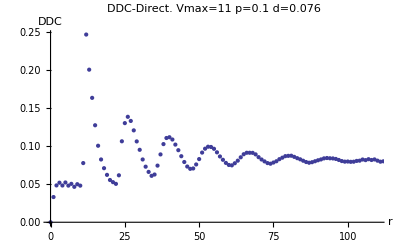

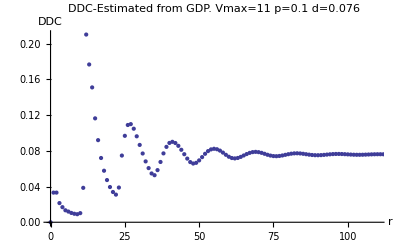

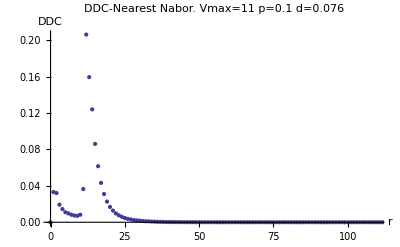

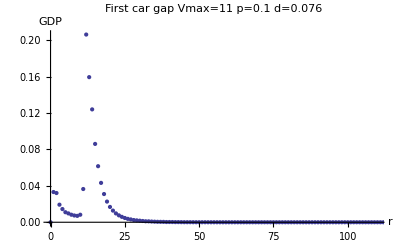

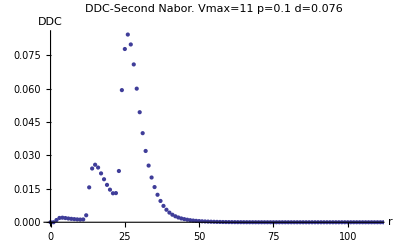

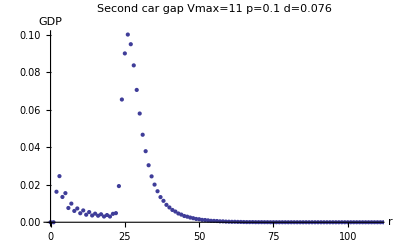

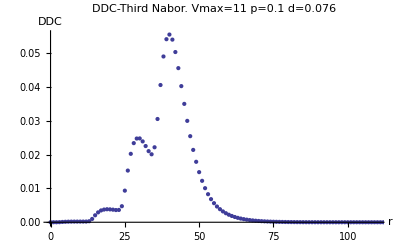

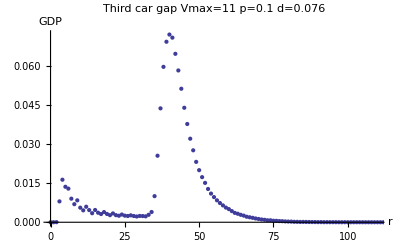

```mathematica
d="0.076";
p="0.1";
vmax="11";
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/ddensitycorrelation.d";
ddc1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDC1.d";ddc2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDC2.d";
ddc3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/DDC3.d";
gap1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/GapD.d.";
gap2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/Gap2D.d.";
gap3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short3/Gap3D.d.";
g=".p"<>p<>".v11.txt";

ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
ddc1add=ddc1<>d<>g;
ddc2add=ddc2<>d<>g;
ddc3add=ddc3<>d<>g;
gap1add=gap1<>d<>g;
gap2add=gap2<>d<>g;
gap3add=gap3<>d<>g;
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
DDC1=ReadList[ddc1add,{Number,Number}];
DDC2=ReadList[ddc2add,{Number,Number}];
DDC3=ReadList[ddc3add,{Number,Number}];
GAP1=ReadList[gap1add,{Number,Number}];
GAP2=ReadList[gap2add,{Number,Number}];
GAP3=ReadList[gap3add,{Number,Number}];
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDC1,PlotLabel->"DDC-Nearest Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP1,PlotLabel->"First car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC2,PlotLabel->"DDC-Second Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP2,PlotLabel->"Second car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[DDC3,PlotLabel->"DDC-Third Nabor.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[GAP3,PlotLabel->"Third car gap   Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP"},PlotRange->{{0,110},Full}]
ListPlot[{DDC,DDC1},PlotLabel->"DDC-(Direct vs. First Nabor).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
SDDC1=DDC1[[All,2]];
SDDC2=DDC2[[All,2]];
SDDC3=DDC3[[All,2]];
SGAP1=GAP1[[All,2]];
SGAP2=GAP2[[All,2]];
SGAP3=GAP3[[All,2]];
Com2=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]},{i,1,220}];
Com3=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]+SDDC3[[i]]},{i,1,220}];
Com2Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]},{i,1,220}];
Com3Gap=Table[{i-1,SGAP1[[i]]+SGAP2[[i]]+SGAP3[[i]]},{i,1,220}];
ListPlot[{DDC,Com2,Com2Gap},PlotLabel->"DDC-(Direct vs. First Two Nabors vs. First Two Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,220},Full}]
ListPlot[{DDC,Com3,DDCC,Com3Gap},PlotLabel->"DDC-(Direct vs. First Three Nabors vs, Estimated vs.  vs. First Three Gaps).  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,10},Full}]
```